```mathematica
Index[p_,t_]:=1+(2.7785 10^-4) *(p(1+p(60.1 - 0.972 t) 10^-10))/(96095.43(1+.003661t));
RE=6.371 10^6;
p[r_]:=QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[r-RE,"Meters"],"Pressure"],"Pascals"]];
t[r_]:=QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[r-RE,"Meters"],"Temperature"],"Celsius"]];
Index[r_]:=1+((2.7785 10^-4) p[r](1+p[r](60.1 - 0.972 t[r])10^-10))/(96095.43(1+.003661t[r]));
<<MaTeX`
```

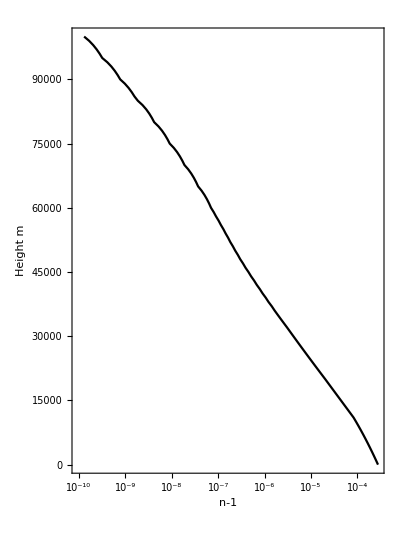

```mathematica
ListLogLinearPlot[
Table[{Index[x+RE]-1,x},{x,0,100000,1000}],AxesLabel->{n-1,Height(m)},Joined->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed],AspectRatio->1.4,Frame->True,FrameStyle->Black, FrameLabel->MaTeX /@ {"n-1","\\text{Height }(m)"},BaseStyle->{Black,FontFamily->"Times"}]
```

```mathematica
Table[{x,r=RE;phi0=x;phi=phi0;theta=0;dr=0;
While[r<RE+100000,
r=r+dr;
dr=Ceiling[r-RE+.01]/10;
theta=theta+Pi/2-phi-ArcSin[r/(r+dr)Cos[phi]];
phi=ArcCos[Index[r]/Index[r+dr]*r/(r+dr)Cos[phi]];];theta-phi+phi0},{x,0,Pi/2,Pi/180}]
(* this one takes a long time! don't run multiple times *)
(* Ceiling[r-RE+0.1]/10 is there to decrease the increment for lower values of r, this increases precision without sacrificing too much computation power*)
```

{{0,0.00928885},{π/180,0.00671692},{π/90,0.0051041},{π/60,0.00404762},{π/45,0.0033197},{π/36,0.002796},{π/30,0.00240515},{(7 π)/180,0.00210427},{(2 π)/45,0.00186651},{π/20,0.00167442},{π/18,0.00151628},{(11 π)/180,0.00138397},{π/15,0.00127171},{(13 π)/180,0.0011753},{(7 π)/90,0.00109161},{π/12,0.00101829},{(4 π)/45,0.000953501},{(17 π)/180,0.000895831},{π/10,0.00084415},{(19 π)/180,0.000797555},{π/9,0.000755313},{(7 π)/60,0.000716825},{(11 π)/90,0.000681596},{(23 π)/180,0.000649213},{(2 π)/15,0.00061933},{(5 π)/36,0.000591655},{(13 π)/90,0.000565937},{(3 π)/20,0.000541964},{(7 π)/45,0.000519553},{(29 π)/180,0.000498543},{π/6,0.000478796},{(31 π)/180,0.000460192},{(8 π)/45,0.000442624},{(11 π)/60,0.000425999},{(17 π)/90,0.000410234},{(7 π)/36,0.000395254},{π/5,0.000380996},{(37 π)/180,0.0003674},{(19 π)/90,0.000354413},{(13 π)/60,0.000341988},{(2 π)/9,0.000330083},{(41 π)/180,0.000318658},{(7 π)/30,0.00030768},{(43 π)/180,0.000297116},{(11 π)/45,0.000286937},{π/4,0.000277117},{(23 π)/90,0.000267631},{(47 π)/180,0.000258457},{(4 π)/15,0.000249576},{(49 π)/180,0.000240967},{(5 π)/18,0.000232614},{(17 π)/60,0.000224501},{(13 π)/45,0.000216612},{(53 π)/180,0.000208935},{(3 π)/10,0.000201455},{(11 π)/36,0.000194162},{(14 π)/45,0.000187044},{(19 π)/60,0.000180091},{(29 π)/90,0.000173293},{(59 π)/180,0.000166641},{π/3,0.000160126},{(61 π)/180,0.000153741},{(31 π)/90,0.000147477},{(7 π)/20,0.000141328},{(16 π)/45,0.000135287},{(13 π)/36,0.000129347},{(11 π)/30,0.000123503},{(67 π)/180,0.000117749},{(17 π)/45,0.000112079},{(23 π)/60,0.000106488},{(7 π)/18,0.000100971},{(71 π)/180,0.0000955236},{(2 π)/5,0.0000901409},{(73 π)/180,0.0000848187},{(37 π)/90,0.0000795527},{(5 π)/12,0.000074339},{(19 π)/45,0.0000691736},{(77 π)/180,0.0000640528},{(13 π)/30,0.000058973},{(79 π)/180,0.0000539306},{(4 π)/9,0.0000489221},{(9 π)/20,0.0000439442},{(41 π)/90,0.0000389937},{(83 π)/180,0.0000340674},{(7 π)/15,0.000029162},{(17 π)/36,0.0000242745},{(43 π)/90,0.0000194019},{(29 π)/60,0.0000145411},{(22 π)/45,9.68916×10^-6},{(89 π)/180,4.84311×10^-6},{π/2,0.}}

```mathematica
list ={{0,0.009288845437527893},{π/180,0.006716917485172922},{π/90,0.005104098924621388},{π/60,0.004047619096787476},{π/45,0.003319698271114793},{π/36,0.0027960007904853784},{π/30,0.002405150770269468},{(7 π)/180,0.0021042687005206617},{(2 π)/45,0.0018665084440626645},{π/20,0.0016744218104807196},{π/18,0.001516281999682595},{(11 π)/180,0.0013839687135049905},{π/15,0.0012717081008925268},{(13 π)/180,0.001175297175766865},{(7 π)/90,0.00109161196259977},{π/12,0.0010182869634970393},{(4 π)/45,0.0009535010368409425},{(17 π)/180,0.0008958311083434589},{π/10,0.0008441501629140036},{(19 π)/180,0.0007975547792399285},{π/9,0.0007553127714212682},{(7 π)/60,0.000716824768048907},{(11 π)/90,0.0006815956160058922},{(23 π)/180,0.000649212817518896},{(2 π)/15,0.0006193300744113395},{(5 π)/36,0.0005916545901712977},{(13 π)/90,0.0005659371707155136},{(3 π)/20,0.000541964433390385},{(7 π)/45,0.0005195526207721901},{(29 π)/180,0.0004985426481097788},{π/6,0.00047879610786882854},{(31 π)/180,0.0004601920230558054},{(8 π)/45,0.0004426241912938167},{(11 π)/60,0.00042599899822703957},{(17 π)/90,0.0004102336066753587},{(7 π)/36,0.0003952544484773224},{π/5,0.0003809959617731007},{(37 π)/180,0.0003673995285103926},{(19 π)/90,0.00035441257608781473},{(13 π)/60,0.0003419878144853561},{(2 π)/9,0.00033008258558275827},{(41 π)/180,0.0003186583059283654},{(7 π)/30,0.00030767998773961747},{(43 π)/180,0.00029711582557434557},{(11 π)/45,0.0002869368384473825},{π/4,0.00027711655891593523},{(23 π)/90,0.0002676307620566032},{(47 π)/180,0.0002584572285565523},{(4 π)/15,0.0002495755369602559},{(49 π)/180,0.00024096688097241525},{(5 π)/18,0.0002326139083805856},{(17 π)/60,0.00022450057863077078},{(13 π)/45,0.00021661203662759476},{(53 π)/180,0.00020893450055470275},{(3 π)/10,0.00020145516201319769},{(11 π)/36,0.00019416209685652053},{(14 π)/45,0.0001870441854152638},{(19 π)/60,0.0001800910409833767},{(29 π)/90,0.00017329294554957464},{(59 π)/180,0.00016664079193629},{π/3,0.00016012603158155336},{(61 π)/180,0.00015374062737638639},{(31 π)/90,0.0001474770108726986},{(7 π)/20,0.00014132804349809014},{(16 π)/45,0.00013528698127474037},{(13 π)/36,0.00012934744265913345},{(11 π)/30,0.0001235033791915363},{(67 π)/180,0.00011774904864325642},{(17 π)/45,0.00011207899040210911},{(23 π)/60,0.00010648800287760274},{(7 π)/18,0.00010097112269291664},{(71 π)/180,0.00009552360550202366},{(2 π)/5,0.00009014090824632781},{(73 π)/180,0.00008481867274312549},{(37 π)/90,0.00007955271041093503},{(5 π)/12,0.00007433898807684969},{(19 π)/45,0.0000691736147335753},{(77 π)/180,0.00006405282911492449},{(13 π)/30,0.00005897298807044926},{(79 π)/180,0.00005393055559577142},{(4 π)/9,0.00004892209249351964},{(9 π)/20,0.00004394424656894991},{(41 π)/90,0.00003899374329763283},{(83 π)/180,0.000034067376931012916},{(7 π)/15,0.000029162001972560248},{(17 π)/36,0.000024274524958789456},{(43 π)/90,0.000019401896548254527},{(29 π)/60,0.00001454110381859941},{(22 π)/45,9.689162741022272*^-6},{(89 π)/180,4.843110853913757*^-6},{π/2,0.}};
```

```mathematica
ref_ang=Transpose[{Range[0,90],list[[All,2]]*3437.75}]
```

{{0,31.9327},{1,23.0911},{2,17.5466},{3,13.9147},{4,11.4123},{5,9.61195},{6,8.26831},{7,7.23395},{8,6.41659},{9,5.75624},{10,5.2126},{11,4.75774},{12,4.37181},{13,4.04038},{14,3.75269},{15,3.50062},{16,3.2779},{17,3.07964},{18,2.90198},{19,2.74179},{20,2.59658},{21,2.46426},{22,2.34316},{23,2.23183},{24,2.1291},{25,2.03396},{26,1.94555},{27,1.86314},{28,1.78609},{29,1.71386},{30,1.64598},{31,1.58203},{32,1.52163},{33,1.46448},{34,1.41028},{35,1.35879},{36,1.30977},{37,1.26303},{38,1.21838},{39,1.17567},{40,1.13474},{41,1.09547},{42,1.05773},{43,1.02141},{44,0.986417},{45,0.952657},{46,0.920048},{47,0.888511},{48,0.857978},{49,0.828384},{50,0.799668},{51,0.771777},{52,0.744658},{53,0.718265},{54,0.692552},{55,0.667481},{56,0.643011},{57,0.619108},{58,0.595738},{59,0.572869},{60,0.550473},{61,0.528522},{62,0.506989},{63,0.48585},{64,0.465083},{65,0.444664},{66,0.424574},{67,0.404792},{68,0.3853},{69,0.366079},{70,0.347113},{71,0.328386},{72,0.309882},{73,0.291585},{74,0.273482},{75,0.255559},{76,0.237802},{77,0.220198},{78,0.202734},{79,0.1854},{80,0.168182},{81,0.151069},{82,0.134051},{83,0.117115},{84,0.100252},{85,0.0834497},{86,0.0666989},{87,0.0499887},{88,0.0333089},{89,0.0166494},{90,0.}}

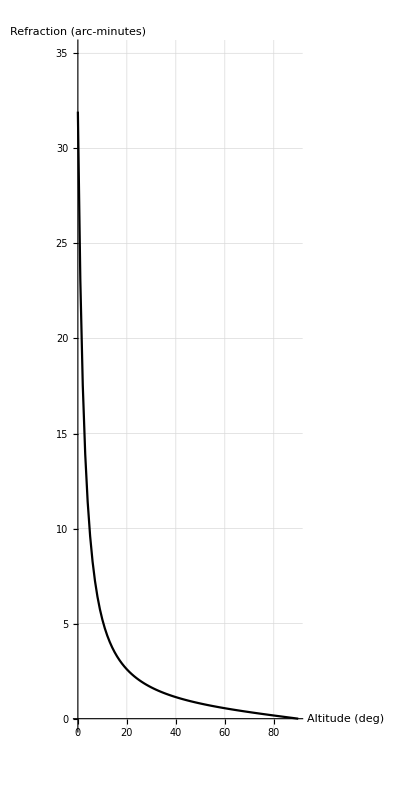

```mathematica
ListLinePlot[{{0,31.932728402861514},{1,23.091083084653214},{2,17.546616078117175},{3,13.914702549981147},{4,11.41229273152488},{5,9.61195171749111},{6,8.268307060493864},{7,7.233949725214905},{8,6.416589403576425},{9,5.756243578980094},{10,5.21259844440884},{11,4.757738444851781},{12,4.371814523843284},{13,4.04037786599254},{14,3.7526890244273594},{15,3.5006160087619467},{16,3.27789818939995},{17,3.079643392707726},{18,2.901977222557616},{19,2.741793942332064},{20,2.5965764799534647},{21,2.4642643463601304},{22,2.343155328924256},{23,2.231831363425585},{24,2.129101963307582},{25,2.0339605673613788},{26,1.945550508627257},{27,1.8631382308877962},{28,1.7860920220595966},{29,1.713864988539392},{30,1.6459813198260653},{31,1.5820251272600951},{32,1.5216313136203183},{33,1.4644780561550053},{34,1.4102805813482142},{35,1.358785980252915},{36,1.3097688675854768},{37,1.263027729136602},{38,1.2183818334458851},{39,1.175668609247033},{40,1.1347414085871272},{41,1.0954675912052383},{42,1.05772687785187},{43,1.0214099293682064},{44,0.9864171163724892},{45,0.9526574504132563},{46,0.9200476522600876},{47,0.8885113374702877},{48,0.8579783021851197},{49,0.8283838950629205},{50,0.7996684635353581},{51,0.7717768641879322},{52,0.7446580289165139},{53,0.7182645792819293},{54,0.6925524832108704},{55,0.6674807484685035},{56,0.6430111484113231},{57,0.6191079761406032},{58,0.5957378235630502},{59,0.572869382478981},{60,0.550473265069485},{61,0.5285218417631723},{62,0.5069890941276196},{63,0.4858504815355594},{64,0.4650828198772387},{65,0.444664171001436},{66,0.42457374181570395},{67,0.40479179197335474},{68,0.3852995492548506},{69,0.3660791318924788},{70,0.34711347703757417},{71,0.3283862748145818},{72,0.30988190732381343},{73,0.29158539222267965},{74,0.2734823302151919},{75,0.25555885626119},{76,0.2378015940503485},{77,0.22019761328983167},{78,0.20273438973918695},{79,0.1853997674993632},{80,0.16818192346959715},{81,0.15106933364240754},{82,0.13405074102143727},{83,0.11711512504458965},{84,0.10025167228116899},{85,0.08344974817707845},{86,0.066698869858762},{87,0.04998867965239012},{88,0.03330891921294932},{89,0.016649404338042018},{90,0.}},AxesLabel->{"Altitude (deg)","Refraction (arc-minutes)"},AspectRatio->2,PlotRange->{Automatic,{0,35}},GridLines->Automatic,GridLinesStyle->Directive[{Black,Dashed}],AxesStyle->Black,BaseStyle->{Black,Medium,FontFamily->"Times"}]
```

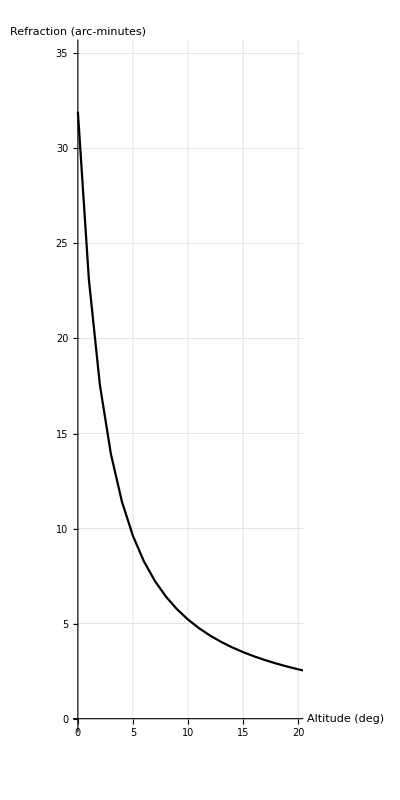

```mathematica
ListLinePlot[{{0,31.932728402861514},{1,23.091083084653214},{2,17.546616078117175},{3,13.914702549981147},{4,11.41229273152488},{5,9.61195171749111},{6,8.268307060493864},{7,7.233949725214905},{8,6.416589403576425},{9,5.756243578980094},{10,5.21259844440884},{11,4.757738444851781},{12,4.371814523843284},{13,4.04037786599254},{14,3.7526890244273594},{15,3.5006160087619467},{16,3.27789818939995},{17,3.079643392707726},{18,2.901977222557616},{19,2.741793942332064},{20,2.5965764799534647},{21,2.4642643463601304},{22,2.343155328924256},{23,2.231831363425585},{24,2.129101963307582},{25,2.0339605673613788},{26,1.945550508627257},{27,1.8631382308877962},{28,1.7860920220595966},{29,1.713864988539392},{30,1.6459813198260653},{31,1.5820251272600951},{32,1.5216313136203183},{33,1.4644780561550053},{34,1.4102805813482142},{35,1.358785980252915},{36,1.3097688675854768},{37,1.263027729136602},{38,1.2183818334458851},{39,1.175668609247033},{40,1.1347414085871272},{41,1.0954675912052383},{42,1.05772687785187},{43,1.0214099293682064},{44,0.9864171163724892},{45,0.9526574504132563},{46,0.9200476522600876},{47,0.8885113374702877},{48,0.8579783021851197},{49,0.8283838950629205},{50,0.7996684635353581},{51,0.7717768641879322},{52,0.7446580289165139},{53,0.7182645792819293},{54,0.6925524832108704},{55,0.6674807484685035},{56,0.6430111484113231},{57,0.6191079761406032},{58,0.5957378235630502},{59,0.572869382478981},{60,0.550473265069485},{61,0.5285218417631723},{62,0.5069890941276196},{63,0.4858504815355594},{64,0.4650828198772387},{65,0.444664171001436},{66,0.42457374181570395},{67,0.40479179197335474},{68,0.3852995492548506},{69,0.3660791318924788},{70,0.34711347703757417},{71,0.3283862748145818},{72,0.30988190732381343},{73,0.29158539222267965},{74,0.2734823302151919},{75,0.25555885626119},{76,0.2378015940503485},{77,0.22019761328983167},{78,0.20273438973918695},{79,0.1853997674993632},{80,0.16818192346959715},{81,0.15106933364240754},{82,0.13405074102143727},{83,0.11711512504458965},{84,0.10025167228116899},{85,0.08344974817707845},{86,0.066698869858762},{87,0.04998867965239012},{88,0.03330891921294932},{89,0.016649404338042018},{90,0.}},AxesLabel->{"Altitude (deg)","Refraction (arc-minutes)"},AspectRatio->2,PlotRange->{{0,20},{0,35}},GridLines->Automatic,GridLinesStyle->Directive[{Black,Dashed}],AxesStyle->Black,BaseStyle->{Black,Medium,FontFamily->"Times"}]
```